```mathematica
Clear[Δ,Ω,γ]

Ω0=1;
Δ0=1;
ham[Δ_,Ω_,γ_]:=Evaluate[{{Δ-I γ,1,Ω/2},{1,Δ+I γ,Ω/2},{Ω/2,Ω/2,0}}];
ham[Δ,Ω0,γ]//MatrixForm

γlist=Table[i,{i,0,2,0.0005}];
γlists=Table[i,{i,1,2,0.0005}];

eigbr1={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[1]]}&/@γlist;
eigbr2={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[2]]}&/@γlist;
eigbr3={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[3]]}&/@γlist;
eigbrs1={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[1]]}&/@γlists;
eigbrs2={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[2]]}&/@γlists;
eigbrs3={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Re][[3]]}&/@γlists;
eigbi1={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[1]]}&/@γlist;
eigbi2={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[2]]}&/@γlist;
eigbi3={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[3]]}&/@γlist;
eigbis1={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[1]]}&/@γlists;
eigbis2={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[2]]}&/@γlists;
eigbis3={#,SortBy[Eigenvalues[ham[Δ0,Ω0,#]],Im][[3]]}&/@γlists;


vecs =Eigenvectors[ham[Δ0,Ω0,1]];
eigvecs={SortBy[vecs,#*Conjugate[#][[1]]&]};

Do[vecs =Eigenvectors[ham[Δ0,Ω0,i]];AppendTo[eigvecs, SortBy[vecs,#*Conjugate[#][[1]]&]],{i,0.0005,2,0.0005}];

eigvec1={(#/2000)^(1/2),eigvecs[[#]][[1]]}&/@Table[i,{i,2,4000,1}];
eigvec2={(#/2000)^(1/2),eigvecs[[#]][[2]]}&/@Table[i,{i,2,4000,1}];
eigvec3={(#/2000)^(1/2),eigvecs[[#]][[3]]}&/@Table[i,{i,2,4000,1}];
hop1 = Re[eigvec1 *Conjugate[eigvec1]];
hop2 = Re[eigvec2 *Conjugate[eigvec2]];
hop3 = Re[eigvec3 *Conjugate[eigvec3]];
```

(-ⅈ γ+Δ | 1 | 1/2
1 | ⅈ γ+Δ | 1/2
1/2 | 1/2 | 0)

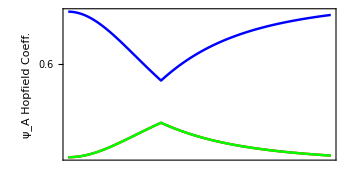

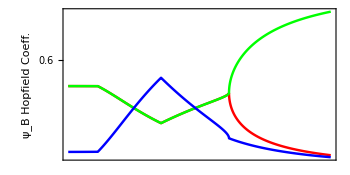

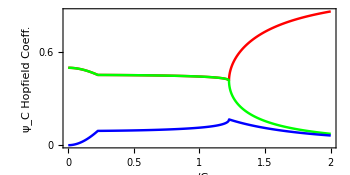

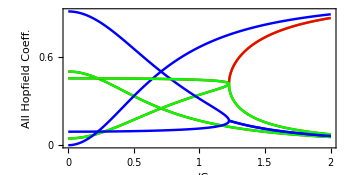

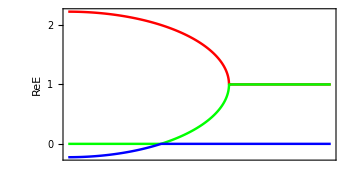

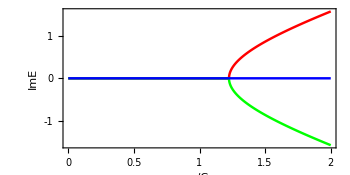

```mathematica
Show[Graphics[{Red,Thickness[0.005],Line[{#[[1]],#[[2]][[1]]}&/@hop1]}],Graphics[{Green,Thickness[0.005],Line[{#[[1]],#[[2]][[2]]}&/@hop1]}],
Graphics[{Blue,Thickness[0.005],Line[{#[[1]],#[[2]][[3]]}&/@hop1]}],
(*
Graphics[{Text[Style["3",FontFamily->"Arial",(*Bold,*)18],{0.15,0.15}]}],Graphics[{Text[Style["2",FontFamily->"Arial",(*Bold,*)18],{0.15,0.4}]}],Graphics[{Text[Style["1",FontFamily->"Arial",(*Bold,*)18],{0.15,0.49}]}],
Graphics[{Text[Style["2",FontFamily->"Arial",(*Bold,*)18],{1.42,0.1}]}],Graphics[{Text[Style["3",FontFamily->"Arial",(*Bold,*)18],{1.59,0.2}]}],Graphics[{Text[Style["1",FontFamily->"Arial",(*Bold,*)18],{1.4,0.75}]}],
*)
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{{0,0.3,0.6,0.9,1},None},{None,None}},FrameLabel->{{"ψ_A Hopfield Coeff.",None},{None,None}},AspectRatio->1/2,ImageSize->{350,Automatic}]

Show[Graphics[{Red,Thickness[0.005],Line[{#[[1]],#[[2]][[1]]}&/@hop2]}],
Graphics[{Green,Thickness[0.005],Line[{#[[1]],#[[2]][[2]]}&/@hop2]}],
Graphics[{Blue,Thickness[0.005],Line[{#[[1]],#[[2]][[3]]}&/@hop2]}],
(*
Graphics[{Text[Style["2",FontFamily->"Arial",(*Bold,*)18],{0.15,0.15}]}],Graphics[{Text[Style["3",FontFamily->"Arial",(*Bold,*)18],{0.15,0.4}]}],Graphics[{Text[Style["1",FontFamily->"Arial",(*Bold,*)18],{0.15,0.49}]}],
Graphics[{Text[Style["1",FontFamily->"Arial",(*Bold,*)18],{1.42,0.1}]}],Graphics[{Text[Style["3",FontFamily->"Arial",(*Bold,*)18],{1.59,0.2}]}],Graphics[{Text[Style["2",FontFamily->"Arial",(*Bold,*)18],{1.4,0.75}]}],
*)
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{{0,0.3,0.6,0.9,1},None},{None,None}},FrameLabel->{{"ψ_B Hopfield Coeff.",None},{None,None}},AspectRatio->1/2,ImageSize->{350,Automatic}]

Show[Graphics[{Red,Thickness[0.005],Line[{#[[1]],#[[2]][[1]]}&/@hop3]}],
Graphics[{Green,Thickness[0.005],Line[{#[[1]],#[[2]][[2]]}&/@hop3]}],
Graphics[{Blue,Thickness[0.005],Line[{#[[1]],#[[2]][[3]]}&/@hop3]}],
(*
Graphics[{Text[Style["1",FontFamily->"Arial",(*Bold,*)18],{0.15,0.15}]}],Graphics[{Text[Style["3",FontFamily->"Arial",(*Bold,*)18],{0.15,0.4}]}],Graphics[{Text[Style["2",FontFamily->"Arial",(*Bold,*)18],{0.15,0.49}]}],
Graphics[{Text[Style["2",FontFamily->"Arial",(*Bold,*)18],{1.42,0.1}]}],Graphics[{Text[Style["1",FontFamily->"Arial",(*Bold,*)18],{1.59,0.2}]}],Graphics[{Text[Style["3",FontFamily->"Arial",(*Bold,*)18],{1.4,0.75}]}],
*)
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{{0,0.3,0.6,0.9,1},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{{"ψ_C Hopfield Coeff.",None},{"γ/C",None}},AspectRatio->1/2,ImageSize->{350,Automatic}]



Show[Graphics[{Red,Thickness[0.005],Line[{#[[1]],#[[2]][[1]]}&/@hop1]}],
Graphics[{Green,Thickness[0.005],Line[{#[[1]],#[[2]][[2]]}&/@hop1]}],
Graphics[{Blue,Thickness[0.005],Line[{#[[1]],#[[2]][[3]]}&/@hop1]}],
Graphics[{Red,Thickness[0.005],Line[{#[[1]],#[[2]][[1]]}&/@hop2]}],
Graphics[{Green,Thickness[0.005],Line[{#[[1]],#[[2]][[2]]}&/@hop2]}],
Graphics[{Blue,Thickness[0.005],Line[{#[[1]],#[[2]][[3]]}&/@hop2]}],
Graphics[{Red,Thickness[0.005],Line[{#[[1]],#[[2]][[1]]}&/@hop3]}],
Graphics[{Green,Thickness[0.005],Line[{#[[1]],#[[2]][[2]]}&/@hop3]}],
Graphics[{Blue,Thickness[0.005],Line[{#[[1]],#[[2]][[3]]}&/@hop3]}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{{0,0.3,0.6,0.9,1},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{{"All Hopfield Coeff.",None},{"γ/C",None}},AspectRatio->1/2,ImageSize->{350,Automatic}]




Show[Graphics[{Red,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbr3]}],
Graphics[{Green,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbr2]}],
Graphics[{Blue,Thickness[0.005],Line[{#[[1]],Re[#[[2]]]}&/@eigbr1]}],
(*Graphics[{Text[Style["+",FontFamily->"Arial",(*Bold,*)18],{0.1,1.75}]}],Graphics[{Text[Style["-",FontFamily->"Arial",(*Bold,*)18],{0.1,0}]}],Graphics[{Text[Style["+",FontFamily->"Arial",(*Bold,*)18],{0.1,-.5}]}],
Graphics[{Text[Style["Δ/C=1",FontFamily->"Arial",(*Bold,*)18],{1.75,2.1}]}],
Graphics[{Text[Style["",FontFamily->"Arial",(*Bold,*)18],{0.1,-1}]}],*)
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{{2,0,1,-1},None},{None,None}},FrameLabel->{None,"ReE"},AspectRatio->1/2,ImageSize->{350,Automatic}]
Show[Graphics[{Red,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbi3]}],Graphics[{Green,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbi1]}],
Graphics[{Blue,Thickness[0.005],Line[{#[[1]],Im[#[[2]]]}&/@eigbi2]}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16,Thickness[0.003]],FrameTicks->{{{-1,0,1},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{"γ/C","ImE"},AspectRatio->1/2,ImageSize->{350,Automatic}]
```